```mathematica
dir=NotebookDirectory[]<>"data\\data.xlsx"
```

## Import

```mathematica
data = Import[dir];
```

## Points

```mathematica
n=7;
points = data⟦1⟧⟦2;;401⟧⟦;;n⟧;
```

## Local outlier factors Algorithm

### 1. k = Amount Of Nearest Neighbours

```mathematica
k=3;
```

### 1. Normalising Data: (ξ-ξ̄)/(√σ)∼N(0,1)

```mathematica
normalise=Standardize[points];
```

### 2. Computing Distance Matrix

```mathematica
distanseM=DistanceMatrix[normalise];
dmDim=Length[distanseM];
```

```mathematica
distanseM//MatrixForm
```

(0. | 4.6138 | 6.29806 | 5.07087 | 5.78926 | 4.59236 | 5.12963
4.6138 | 0. | 4.75301 | 3.27147 | 4.83792 | 4.81528 | 3.89398
6.29806 | 4.75301 | 0. | 4.84456 | 4.96059 | 5.41616 | 3.68337
5.07087 | 3.27147 | 4.84456 | 0. | 4.2818 | 4.34275 | 4.05986
5.78926 | 4.83792 | 4.96059 | 4.2818 | 0. | 3.49417 | 4.10716
4.59236 | 4.81528 | 5.41616 | 4.34275 | 3.49417 | 0. | 5.06291
5.12963 | 3.89398 | 3.68337 | 4.05986 | 4.10716 | 5.06291 | 0.)

### 4. Rank

```mathematica
ranked= Ordering/@Ordering/@distanseM-1;
rnkDim=Length@ranked;
ranked//MatrixForm
```

(0 | 2 | 6 | 3 | 5 | 1 | 4
3 | 0 | 4 | 1 | 6 | 5 | 2
6 | 2 | 0 | 3 | 4 | 5 | 1
6 | 1 | 5 | 0 | 3 | 4 | 2
6 | 4 | 5 | 3 | 0 | 1 | 2
3 | 4 | 6 | 2 | 1 | 0 | 5
6 | 2 | 1 | 3 | 4 | 5 | 0)

### 5. K-nearest Distanse

```mathematica
ranked//MatrixForm
```

(0 | 2 | 6 | 3 | 5 | 1 | 4
3 | 0 | 4 | 1 | 6 | 5 | 2
6 | 2 | 0 | 3 | 4 | 5 | 1
6 | 1 | 5 | 0 | 3 | 4 | 2
6 | 4 | 5 | 3 | 0 | 1 | 2
3 | 4 | 6 | 2 | 1 | 0 | 5
6 | 2 | 1 | 3 | 4 | 5 | 0)

```mathematica
neighRank=ranked/.{k->1,_Integer->0}
neighRank//MatrixForm
```

{{0,0,0,1,0,0,0},{1,0,0,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,1,0,0,0},{1,0,0,0,0,0,0},{0,0,0,1,0,0,0}}

(0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
kdistance =Select[Flatten[neighRank*distanseM],#>0&];
knDim = Length[kdistance];
kdistance//MatrixForm
```

```mathematica
({{5.070869808387158}, {4.613803811778254}, {4.844560806694623}, {4.281795243564671}, {4.281795243564671}, {4.592361638434003}, {4.059864084998952}})
```

{5.07087,4.6138,4.84456,4.2818,4.2818,4.59236,4.05986}

### 6. Reachability Distance

```mathematica
reachDistance=Table[If[distanseM⟦i,j⟧<kdistance⟦j⟧,kdistance⟦j⟧,distanseM⟦i,j⟧],{i,dmDim},{j,knDim}];
reachDistance//MatrixForm
```

(5.07087 | 4.6138 | 6.29806 | 5.07087 | 5.78926 | 4.59236 | 5.12963
5.07087 | 4.6138 | 4.84456 | 4.2818 | 4.83792 | 4.81528 | 4.05986
6.29806 | 4.75301 | 4.84456 | 4.84456 | 4.96059 | 5.41616 | 4.05986
5.07087 | 4.6138 | 4.84456 | 4.2818 | 4.2818 | 4.59236 | 4.05986
5.78926 | 4.83792 | 4.96059 | 4.2818 | 4.2818 | 4.59236 | 4.10716
5.07087 | 4.81528 | 5.41616 | 4.34275 | 4.2818 | 4.59236 | 5.06291
5.12963 | 4.6138 | 4.84456 | 4.2818 | 4.2818 | 5.06291 | 4.05986)

### 7. Расстояние Махаланобиса

```mathematica
ranked//MatrixForm
```

(0 | 2 | 6 | 3 | 5 | 1 | 4
3 | 0 | 4 | 1 | 6 | 5 | 2
6 | 2 | 0 | 3 | 4 | 5 | 1
6 | 1 | 5 | 0 | 3 | 4 | 2
6 | 4 | 5 | 3 | 0 | 1 | 2
3 | 4 | 6 | 2 | 1 | 0 | 5
6 | 2 | 1 | 3 | 4 | 5 | 0)

```mathematica
group1=ranked-k/.{_?Negative->1,_?Positive->0,0->1};
group2=ranked/.{_?Positive->1,_?Integer->0};
```

```mathematica
group1//MatrixForm
group2//MatrixForm
```

(1 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 0 | 0 | 1)

(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0)

### 8. Average Reachability

```mathematica
dummy=group1*group2*reachDistance;
avgreach=(Total[#]&/@dummy)/k;
avgDim=Length@avgreach;
```

```mathematica
avgreach//MatrixForm
```

(4.75901
4.47084
4.55248
4.31849
4.32711
4.56514
4.58005)

### 9. Local Outlier Factors: Metric Result

```mathematica
name=Range[1,n];
f[x_,y_]:=Thread[{x,y}]
```

```mathematica
dummy2=Table[(group1[[i]]*group2[[i]]*avgreach[[i]]/avgreach),{i,avgDim}];
results=(Total[#]&/@(dummy2))/k;
```

```mathematica
lofResult=Thread[{name,results}];
```

```mathematica
lofResult//MatrixForm
```

(1 | 1.06964
2 | 0.983628
3 | 1.02214
4 | 0.96894
5 | 0.964875
6 | 1.0238
7 | 1.03035)

## Lof Function

```mathematica
Clear[lof]
lof[data_,kN_,n_]:=Module[{names=Range[1,n]},
points = data⟦1⟧⟦2;;401⟧⟦;;n⟧;
normalise=Standardize[points];
distanseM=DistanceMatrix[normalise];dmDim=Length[distanseM];
ranked= Ordering/@Ordering/@distanseM-1;rnkDim=Length@ranked;
neighRank=ranked/.{kN->1,_Integer->0};
kdistance =Select[Flatten[neighRank*distanseM],#>0&];knDim = Length[kdistance];
reachDistance=Table[If[distanseM⟦i,j⟧<kdistance⟦j⟧,kdistance⟦j⟧,distanseM⟦i,j⟧],{i,dmDim},{j,knDim}];
group1=ranked-kN/.{_?Negative->1,_?Positive->0,0->1};
group2=ranked/.{_?Positive->1,_?Integer->0};
dummy=group1*group2*reachDistance;
avgreach=(Total[#]&/@dummy)/kN;avgDim=Length@avgreach;
dummy2=Table[(group1[[i]]*group2[[i]]*avgreach[[i]]/avgreach),{i,avgDim}];
results=(Total[#]&/@(dummy2))/kN;
Thread[{names,results}]
]
```

```mathematica
n=200;
k=3;
lofResult=lof[data,k,n];
```

## Dimension Reduction (for Visualisation Points in 2D Dimension)

### 1. Reduction

```mathematica
name = Range[1,n];
visual=Flatten@ DimensionReduce[normalise,1,Method->"PrincipalComponentsAnalysis"];
vis=Thread[{name,visual}];
```

### 2. Anomaly Per Criteria ( Red Points >1.5)

```mathematica
anomaly=Select[lofResult[[All,2]],#>1.5&];
indexOfAnonaly=Flatten@Table[Position[lofResult[[All,2]],anomaly[[i]]],{i,1,Length[anomaly]}]
red=vis[[indexOfAnonaly]];
lofResult[[indexOfAnonaly]]
```

{154}

{{154,1.66689}}

### 3. Visualisation

```mathematica
Clear[visualisation]
visualisation[vis_,red_,n_]:=If[red≠{},ListPlot[{Labeled[#,#]&/@Table[vis[[u]],{u,n}],red},PlotStyle->{{PointSize[Medium],Blue},{PointSize[Large],Red}},ImageSize->1000],Print["no anomalies"];ListPlot[{Labeled[#,#]&/@Table[vis[[u]],{u,n}]},PlotStyle->{{PointSize[Medium]},{PointSize[Large],Red}},ImageSize->1000]]
```

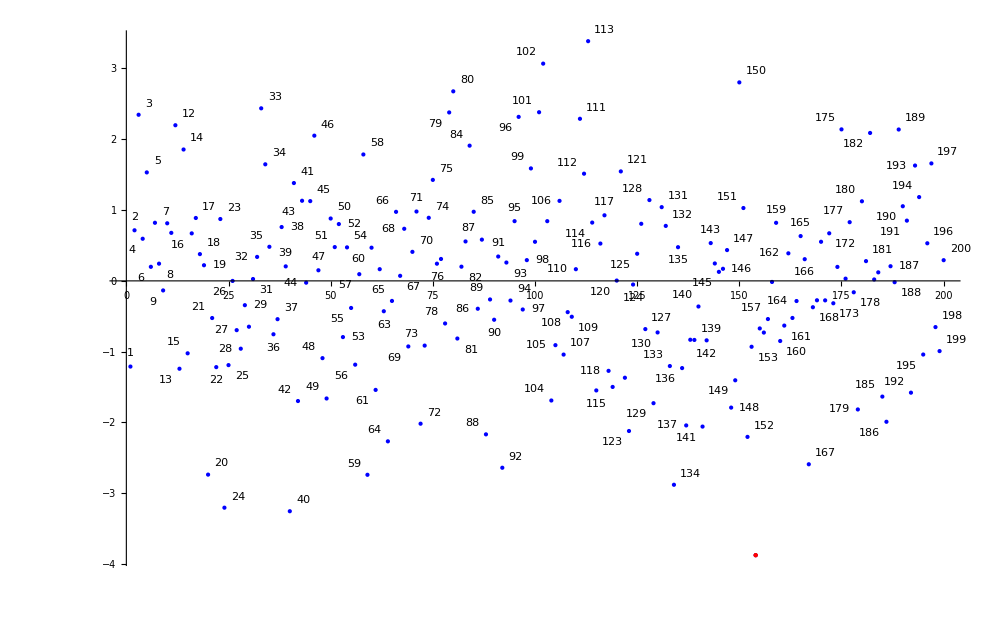

```mathematica
visualisation[vis,red,n]
```